```mathematica
Quit
Clear["Global`*"]
```

```mathematica
MatrixForm[Subscript[H, a]=({{0, 0, -1/2 ⅇ^(ⅈ*Subscript[ω, c]*t)*ℏ*Subscript[Ω, c]}, {0, ℏ*Subscript[ω, 2], -1/2 ⅇ^(ⅈ*Subscript[ω, p]*t)*ℏ*Subscript[Ω, p]}, {-1/2 ⅇ^(-ⅈ*Subscript[ω, c]*t)*ℏ*Subscript[Ω, c], -1/2 ⅇ^(-ⅈ*Subscript[ω, p]*t)*ℏ*Subscript[Ω, p], ℏ*Subscript[ω, 3]}})];
MatrixForm[Subscript[Γ, a]=({{0, 0, 0}, {0, Γ, 0}, {0, 0, κ}})];
MatrixForm[Subscript[ρ̃, a]=({{Subscript[ρ̃, 11], Subscript[ρ̃, 12], Subscript[ρ̃, 13]}, {Subscript[ρ̃, 21], Subscript[ρ̃, 22], Subscript[ρ̃, 23]}, {Subscript[ρ̃, 31], Subscript[ρ̃, 32], Subscript[ρ̃, 33]}})];
MatrixForm[Subscript[ρ, a]=({{Subscript[ρ̃, 11], Subscript[ρ̃, 12], Subscript[ρ̃, 13]}, {Subscript[ρ̃, 21], Subscript[ρ̃, 22], Subscript[ρ̃, 23]}, {Subscript[ρ̃, 31], Subscript[ρ̃, 32], Subscript[ρ̃, 33]}})({{1, ⅇ^(-ⅈ*(Subscript[ω, p]-Subscript[ω, c])*t), ⅇ^(ⅈ*Subscript[ω, c]*t)}, {ⅇ^(ⅈ*(Subscript[ω, p]-Subscript[ω, c])*t), 1, ⅇ^(ⅈ*Subscript[ω, p]*t)}, {ⅇ^(-ⅈ*Subscript[ω, c]*t), ⅇ^(-ⅈ*Subscript[ω, p]*t), 1}})];
MatrixForm[B=({{Subscript[ρ̃, 22]*Γ, 0, 0}, {0, Subscript[ρ̃, 33]*κ, 0}, {0, 0, 0}})];
MatrixForm[Simplify[Subscript[ρ̇, a]=D[Subscript[ρ, a], t]]];
MatrixForm[
Simplify[G=1/(ⅈ *ℏ)*(Subscript[H, a].Subscript[ρ, a]-Subscript[ρ, a].Subscript[H, a])-1/2(Subscript[Γ, a].Subscript[ρ, a]+Subscript[ρ, a].Subscript[Γ, a])+B]];
Simplify[Subscript[ρ̇, a]-G]//MatrixForm
Simplify[Tr[Subscript[ρ̇, a]]-Tr[G]]

t=0;
sol=Resolve[
Subscript[ρ̇, a]==G && Subscript[ρ̃, 11]+Subscript[ρ̃, 22]+Subscript[ρ̃, 33]==1  
,{Subscript[ρ̃, 11],Subscript[ρ̃, 12],Subscript[ρ̃, 13],Subscript[ρ̃, 21],Subscript[ρ̃, 22],Subscript[ρ̃, 23],Subscript[ρ̃, 31],Subscript[ρ̃, 32],Subscript[ρ̃, 33]}
];
A=Solve[sol 
,{Subscript[ρ̃, 11],Subscript[ρ̃, 12],Subscript[ρ̃, 13],Subscript[ρ̃, 21],Subscript[ρ̃, 22],Subscript[ρ̃, 23],Subscript[ρ̃, 31],Subscript[ρ̃, 32],Subscript[ρ̃, 33]}
]
```

(-Γ (ρ̃)_22+1/2 ⅈ Ω_c ((ρ̃)_13-(ρ̃)_31) | 1/2 ⅇ^(ⅈ t (ω_c-ω_p)) ((Γ-2 ⅈ ω_2+2 ⅈ ω_c-2 ⅈ ω_p) (ρ̃)_12+ⅈ (Ω_p (ρ̃)_13-Ω_c (ρ̃)_32)) | 1/2 ⅈ ⅇ^(ⅈ t ω_c) (Ω_p (ρ̃)_12+(-ⅈ κ-2 ω_3+2 ω_c) (ρ̃)_13+Ω_c ((ρ̃)_11-(ρ̃)_33))
1/2 ⅇ^(-ⅈ t (ω_c-ω_p)) ((Γ+2 ⅈ ω_2-2 ⅈ ω_c+2 ⅈ ω_p) (ρ̃)_21+ⅈ (Ω_c (ρ̃)_23-Ω_p (ρ̃)_31)) | Γ (ρ̃)_22+1/2 ⅈ Ω_p ((ρ̃)_23-(ρ̃)_32)-κ (ρ̃)_33 | 1/2 ⅈ ⅇ^(ⅈ t ω_p) (Ω_c (ρ̃)_21+(-ⅈ Γ-ⅈ κ+2 ω_2-2 ω_3+2 ω_p) (ρ̃)_23+Ω_p ((ρ̃)_22-(ρ̃)_33))
-1/2 ⅈ ⅇ^(-ⅈ t ω_c) (Ω_p (ρ̃)_21+(ⅈ κ-2 ω_3+2 ω_c) (ρ̃)_31+Ω_c ((ρ̃)_11-(ρ̃)_33)) | -1/2 ⅈ ⅇ^(-ⅈ t ω_p) (Ω_c (ρ̃)_12+(ⅈ Γ+ⅈ κ+2 ω_2-2 ω_3+2 ω_p) (ρ̃)_32+Ω_p ((ρ̃)_22-(ρ̃)_33)) | -1/2 ⅈ (Ω_c ((ρ̃)_13-(ρ̃)_31)+Ω_p ((ρ̃)_23-(ρ̃)_32)+2 ⅈ κ (ρ̃)_33))

0

{{(ρ̃)_11→1-(ⅈ κ 2 Ω_p^2 (-κ (1-1)+1))/1+1,7,(ρ̃)_33→1/1+1/1}}
 |  |  |  |

```mathematica
Subscript[ω, 3]=2*5.34*10^9;
Subscript[ω, 2] = 4.37*10^9;
Subscript[ω, c]=Subscript[ω, 3];
Subscript[ω, p]=-δ*10^6+(Subscript[ω, 3]-Subscript[ω, 2]);
Γ = 0.1*10^6;
κ=7*10^6(*decay rate by Seck's RB87 data*);
Subscript[Ω, p]=1*10^6;
Subscript[Ω, c]=0.2*10^6;
Rhore=Table[{δ,Re[A[[1,8,2]]]},{δ,-10,10,0.05}];
ListPlot[Rhore,PlotRange->All]
Rhoim=Table[{δ,Im[A[[1,8,2]]]},{δ,-10,10,0.05}];
ListPlot[Rhoim,PlotRange->All]
Subscript[Ω, p]=1*10^6;
Subscript[Ω, c]=2*10^6;
Rh1=Table[{δ,Re[A[[1,1,2]]]},{δ,-10,10,0.05}];
ListPlot[Rh1,PlotRange->All]
Rh2=Table[{δ,Re[A[[1,5,2]]]},{δ,-10,10,0.05}];
ListPlot[Rh2,PlotRange->All]
```

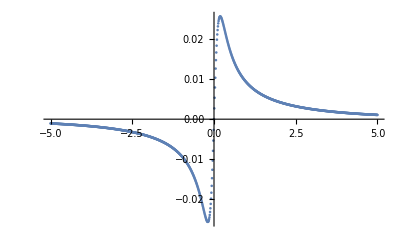

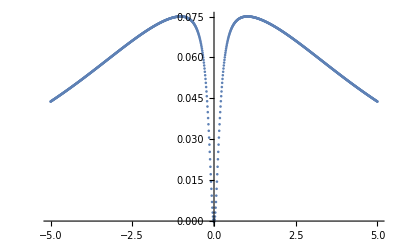

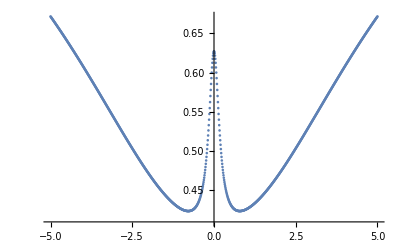

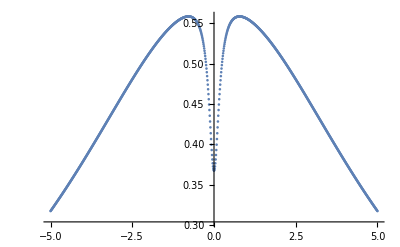

```mathematica
Subscript[ω, 3]=2*5.34*10^9;
Subscript[ω, 2] = 4.37*10^9;
Subscript[ω, c]=Subscript[ω, 3]-δ*10^6;
Subscript[ω, p]=(Subscript[ω, 3]-Subscript[ω, 2]);
Γ = 0.1*10^6;
κ=7*10^6(*decay rate by Seck's RB87 data*);
Subscript[Ω, p]=1*10^6;
Subscript[Ω, c]=1*10^6;
Rhore=Table[{δ,Re[A[[1,8,2]]]},{δ,-5,5,0.01}];
ListPlot[Rhore,PlotRange->All]
Rhoim=Table[{δ,Im[A[[1,8,2]]]},{δ,-5,5,0.01}];
ListPlot[Rhoim,PlotRange->All]
Rh1=Table[{δ,Re[A[[1,1,2]]]},{δ,-5,5,0.01}];
ListPlot[Rh1,PlotRange->All]
Rh2=Table[{δ,Re[A[[1,5,2]]]},{δ,-5,5,0.01}];
ListPlot[Rh2,PlotRange->All]
```